45 °

9.81

vo/(√2)

m (1-x)

m x

(m vo)/(√2)

-m v1 (1-x)

m v2 x

Solve::bdomv: Warning: v1 is not a valid domain specification. Assuming it is a variable to eliminate.

{{v2→-(-2 √2 vo+√2 vo x)/(2 x)}}

0.101937 vo^2

0.0254842 vo^2

-(0.0360401 √(vo^2) (-2 √2 vo+√2 vo x))/x

0.0509684 vo^2-(0.0360401 √(vo^2) (-2 √2 vo+√2 vo x))/x

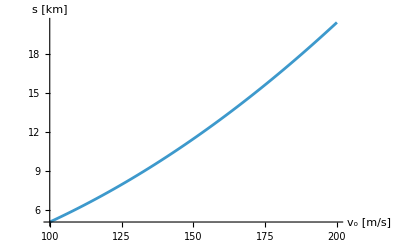

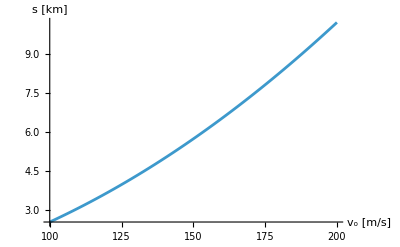

```mathematica
ClearAll["Global`*"]
a=45°
g=9.81
vx=vo*Cos[a]
m1=(1-x)*m
m2=x*m
pp=m*vx
p1=-m1*v1
p2=m2*v2
A=Solve[{p1+p2==pp,v1==vx},v2,v1]
zasiegUk=(vo^2*Sin[2*a])/g
hmax=(vo^2*Sin[a]^2)/(2*g)
zasiegPoz=v2*√((2*hmax)/g)/.A[[1,1]]
s=1/2*zasiegUk+zasiegPoz
Plot[s*10^-3/.x->0.2,{vo,100,200},AxesLabel->{"v_o [m/s]","s [km] "}]
Plot[s*10^-3/.x->0.4,{vo,100,200},AxesLabel->{"v_o [m/s]","s [km] "}]
```